(-1 | -1 | 0
1 | -1 | -1
0 | 1 | -1)

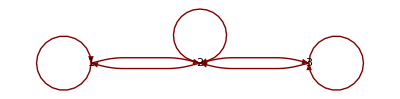

(2/3 | -1/3 | 1/3
1/3 | 1/3 | -1/3
1/3 | 1/3 | 2/3)

```mathematica
(* Trophic Chain - Qualitative w/ self-limitation in all species *)
Clear["Global`*"]
A={{-1,-1,0},{1,-1,-1},{0,1,-1}};
A//MatrixForm
GraphPlot[A,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->All,MultiedgeStyle->All,EdgeLabeling->True]

-Inverse[A]//MatrixForm
```

(-1 | -1 | 0
1 | 0 | -1
0 | 1 | 0)

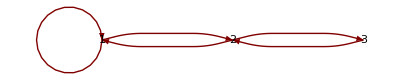

(1 | 0 | 1
0 | 0 | -1
1 | 1 | 1)

```mathematica
(* Trophic Chain - Qualitative w/ basal self-limitation only*)
Clear["Global`*"]
A={{-1,-1,0},{1,0,-1},{0,1,0}};
A//MatrixForm
GraphPlot[A,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->All,MultiedgeStyle->All,EdgeLabeling->True]

-Inverse[A]//MatrixForm
```

```mathematica
(* Trophic Chain w/ Symbolics  - with self-limitation in all species *)
Clear["Global`*"]

A={{-Subscript[Α, 11],-Subscript[Α, 12],0},{Subscript[Α, 21],-Subscript[Α, 22],-Subscript[Α, 23]},{0,Subscript[Α, 32],-Subscript[Α, 33]}};
Inverse[A]  //MatrixForm
GraphPlot[A,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->All,MultiedgeStyle->All,EdgeLabeling->True]
```

((Α_23 Α_32+Α_22 Α_33)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | -(Α_12 Α_33)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | (Α_12 Α_23)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33)
(Α_21 Α_33)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | (Α_11 Α_33)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | -(Α_11 Α_23)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33)
(Α_21 Α_32)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | (Α_11 Α_32)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33) | (Α_12 Α_21+Α_11 Α_22)/(-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33))

-Graphics-

```mathematica
Det[A]
```

-Α_11 Α_23 Α_32-Α_12 Α_21 Α_33-Α_11 Α_22 Α_33

```mathematica
AdjA=-Inverse[A] * -Det[A]//FullSimplify//MatrixForm
```

(Α_23^2 | -Α_13 Α_23 | Α_12 Α_23
-Α_23 Α_31 | Α_13 Α_31 | -Α_13 Α_21-Α_11 Α_23
Α_21 Α_23 | Α_11 Α_23-Α_12 Α_31 | Α_12 Α_21)

```mathematica
NormalizedInverse[A_]:=Transpose[Transpose[Inverse[A]]/Diagonal[Inverse[A]]];

NormalizedInverse[A]//MatrixForm
```

(1 | -Α_23/Α_31 | Α_23/Α_21
-Α_31/Α_23 | 1 | (-Α_13 Α_21-Α_11 Α_23)/(Α_12 Α_21)
Α_21/Α_23 | (Α_11 Α_23-Α_12 Α_31)/(Α_13 Α_31) | 1)

(1 | -Α_23/Α_31 | Α_23/Α_21
-Α_31/Α_23 | 1 | (-Α_13 Α_21-Α_11 Α_23)/(Α_12 Α_21)
Α_21/Α_23 | (Α_11 Α_23-Α_12 Α_31)/(Α_13 Α_31) | 1)

(-Α_11 | -Α_12 | -Α_13
Α_21 | 0 | -Α_23
Α_31 | Α_23 | 0)

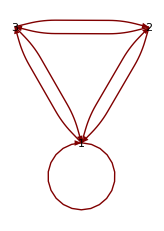

```mathematica
(* Intraguild predation with basal-only self-limitation )*)
Clear["Global`*"]
A={{-Subscript[Α, 11],-Subscript[Α, 12],-Subscript[Α, 13]},{Subscript[Α, 21],0,-Subscript[Α, 23]},{Subscript[Α, 31],Subscript[Α, 23],0}};
A//MatrixForm
GraphPlot[A,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->All,MultiedgeStyle->All,EdgeLabeling->True]
```

```mathematica
AdjA=Simplify[-Inverse[A]  * -Det[A]];
AdjA//MatrixForm
```

(Α_23^2 | -Α_13 Α_23 | Α_12 Α_23
-Α_23 Α_31 | Α_13 Α_31 | -Α_13 Α_21-Α_11 Α_23
Α_21 Α_23 | Α_11 Α_23-Α_12 Α_31 | Α_12 Α_21)

(-Α_11 | -Α_12 | -Α_13
Α_21 | -Α_22 | -Α_23
Α_31 | Α_32 | -Α_33)

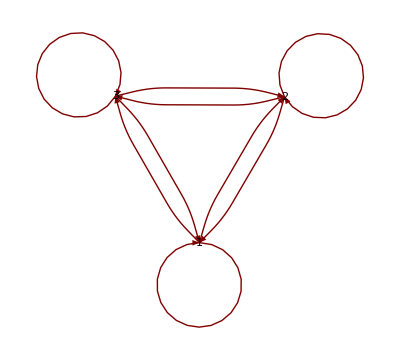

```mathematica
(* Full matrix w/ Symbolics (= IGP with self-limitation in all species )*)
Clear["Global`*"]
A={{-Subscript[Α, 11],-Subscript[Α, 12],-Subscript[Α, 13]},{Subscript[Α, 21],-Subscript[Α, 22],-Subscript[Α, 23]},{Subscript[Α, 31],Subscript[Α, 32],-Subscript[Α, 33]}};
A//MatrixForm
GraphPlot[A,VertexLabeling->True,DirectedEdges->True,SelfLoopStyle->All,MultiedgeStyle->All,EdgeLabeling->True]
```

```mathematica
-Inverse[A]//MatrixForm
```

(-(α_23 α_32+α_22 α_33)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(-α_13 α_32-α_12 α_33)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(-α_13 α_22+α_12 α_23)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33)
-(-α_23 α_31+α_21 α_33)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(α_13 α_31+α_11 α_33)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(-α_13 α_21-α_11 α_23)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33)
-(α_22 α_31+α_21 α_32)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(-α_12 α_31+α_11 α_32)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33) | -(α_12 α_21+α_11 α_22)/(-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33))

```mathematica
Det[A]
```

-α_13 α_22 α_31+α_12 α_23 α_31-α_13 α_21 α_32-α_11 α_23 α_32-α_12 α_21 α_33-α_11 α_22 α_33

```mathematica
AdjA=Simplify[-Inverse[A]  * -Det[A]];
AdjA//MatrixForm
```

(α_23 α_32+α_22 α_33 | -α_13 α_32-α_12 α_33 | -α_13 α_22+α_12 α_23
-α_23 α_31+α_21 α_33 | α_13 α_31+α_11 α_33 | -α_13 α_21-α_11 α_23
α_22 α_31+α_21 α_32 | -α_12 α_31+α_11 α_32 | α_12 α_21+α_11 α_22)